# Graviton Basis Toolkit Mathematical Background

This notebook is the notebook and PDF rendering of graviton_basis_toolkit_mathematical_background.md. It explains the quotient spaces and linear maps behind the toolkit, independently of the implementation details.

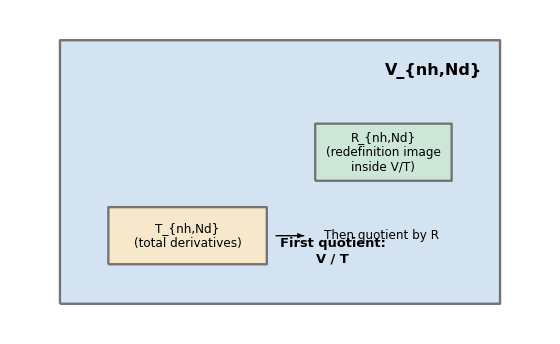

## Operator Spaces

For each pair {nh, Nd}, the toolkit studies the finite-dimensional vector space V_{nh,Nd} of local scalar operators built from nh gravitons, Nd derivatives, and the flat metric, modulo only canonical tensor identities. The entire computation is organized sector by sector because both IBP and the field-redefinition map preserve this grading.

### Raw Spanning Set

A raw spanning set is built by distributing Nd derivatives among nh gravitons in all ordered ways, forming the corresponding monomials, and contracting all indices. Canonicalization then removes duplicates. This produces an explicit spanning set of V_{nh,Nd}.

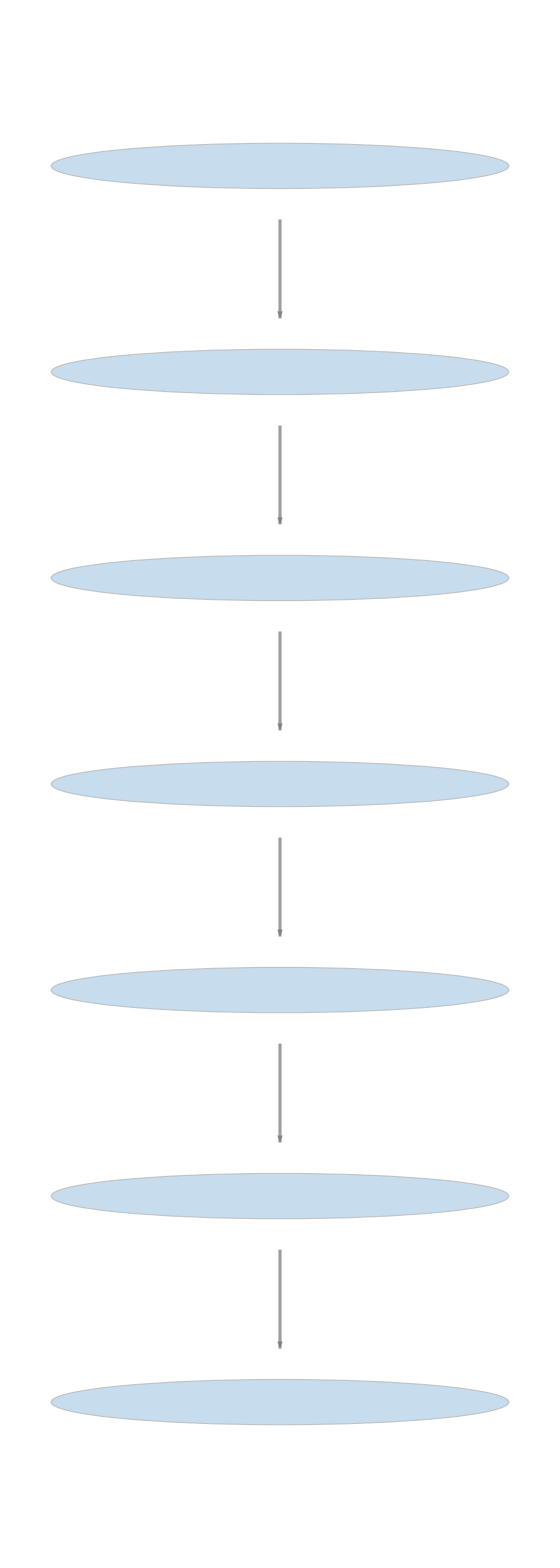

## IBP as a Kernel Quotient

The subspace T_{nh,Nd} of total derivatives is identified using the Euler operator. A local scalar density is a total derivative if and only if its Euler-Lagrange derivative with respect to h_{mu nu} vanishes. Therefore the IBP problem is exactly the kernel problem ker(E), where E is the Euler map from V_{nh,Nd} into a rank-2 tensor space.

The first quotient is therefore V_{nh,Nd} / T_{nh,Nd}. In the code this is the space represented by the IBP basis.

## Field Redefinitions as an Image Quotient

A local field redefinition h_{mu nu} -> h_{mu nu} + Delta h_{mu nu} changes the Fierz-Pauli action by E_FP^{mu nu} Delta h_{mu nu} plus a total derivative. This means the physically redundant directions form the image of a linear map from rank-2 tensors Delta h into the scalar IBP quotient.

For scalar sector {nh, Nd}, the source of this map is the rank-2 space with labels {nh-1, Nd-2}. The quadratic kinetic operator supplies the extra field and the extra two derivatives.

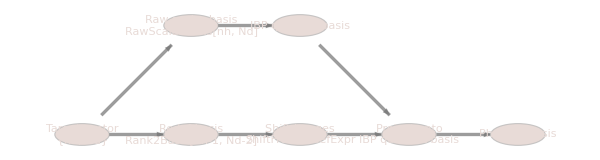

## Final Quotient Space

The final interaction basis is the double quotient (V_{nh,Nd} / T_{nh,Nd}) / R_{nh,Nd}, where R_{nh,Nd} is the field-redefinition image inside the IBP quotient. This is the precise meaning of the toolkit's PhysicalBasis for nh >= 3.

## Why Quadratic Sectors Are Different

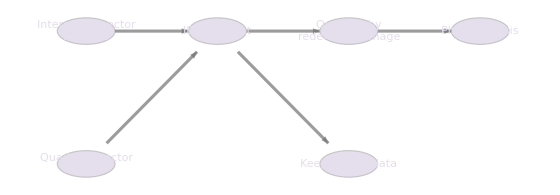

At quadratic order, quotienting by linear field redefinitions removes directions that act directly on the kinetic operator itself, including simple rescalings. That is mathematically legitimate but usually not the desired equivalence relation for the kinetic term. The toolkit therefore keeps quadratic sectors modulo IBP only.

## Relation to Gauge Invariance

The toolkit does not automatically impose linearized diffeomorphism invariance. Its quotients are by total derivatives and field redefinitions, not by gauge symmetry. This is why the off-shell quadratic four-derivative space is larger than the curvature-squared gauge-invariant subspace.

## Why the Validation Matters

The reducer has been tested on expanded Lagrangians that are known to be of the form E_FP^{mu nu} Delta h_{mu nu}. The strongest stored test builds such an expression in sector {3,4}, expands it to 240 scalar terms, and still reduces it to exactly zero. That confirms that the implemented image quotient matches the mathematical one in a genuinely nontrivial case.

## Takeaway

IBP reduction is a kernel quotient.

Field-redefinition removal is an image quotient.

The toolkit is a sector-wise linear algebra realization of those two facts.